```mathematica
nu=InverseCDF[NormalDistribution[0,1],0.975]*10
```

19.5996

```mathematica
pwra[x_]:=1-CDF[NormalDistribution[x,10],nu]+CDF[NormalDistribution[x,10],-nu]
```

```mathematica
pwra[0]
```

0.05

```mathematica
?pwr_a
```

Information::nomatch: No symbol matching "pwr_a" found.

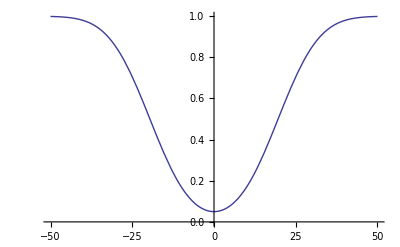

```mathematica
Plot[pwra[x],{x,-50,50}]
```

```mathematica
nub=InverseCDF[NormalDistribution[0,1],0.975]*Sqrt[200]
```

27.7181

```mathematica
pwrb[x_]:=1-CDF[NormalDistribution[x,Sqrt[200]],nub]+CDF[NormalDistribution[x,Sqrt[200]],-nub]
```

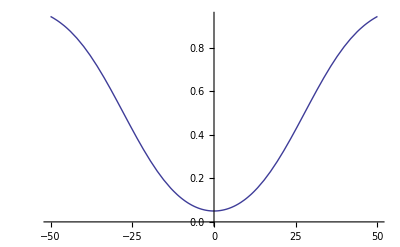

```mathematica
Plot[pwrb[x],{x,-50,50}]
```

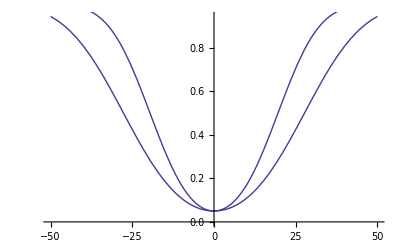

```mathematica
Show[%18,%15]
```